The generalized Lane Emden equation is reduced to the following system of 1st order ODEs:
 h'(x) = Piecewise[{{0, x=0}, {(-m(x))/x^2, x>0}}] 
 m'(x)=(h(x)+1) x^2
 h(0) = 1
m(0)=0
 
 This system is integrated using the 3rd - order Runge-Kutta method, and the results are tabulated below:

```mathematica
hp[x_,m_] := Piecewise[{{-m/x^2,x>0},{0,x==0}}] (*function for h'(x)*)
mp[x_,h_] := (h+1)x^2 (*function for m'(x)*)

M= 120;
Δx = 2/M;
(*Arrays to store values for x,h,m,e*)
x = Range[0,2,Δx]; 
h = ConstantArray[0.,M+1]; h[[1]] = 1.;
m = ConstantArray[0.,M+1];
e = ConstantArray[0.,M+1]; e[[1]] = h[[1]]-(2Sinc[x[[1]]]-1);

(*Loop using Runge-Kutta method*)
Do[
p1=Δx hp[x⟦n⟧,m⟦n⟧] ; q1=Δx mp[x⟦n⟧,h⟦n⟧];p2=Δx hp[x⟦n⟧+Δx/3,m⟦n⟧+q1/3]; q2=Δx mp[x⟦n⟧+Δx/3,h⟦n⟧+p1/3];  
p3=Δx hp[x⟦n⟧+(2 Δx)/3,m⟦n⟧+(2 q2)/3]; q3=Δx mp[x⟦n⟧+(2 Δx)/3,h⟦n⟧+(2 p2)/3];h⟦n+1⟧=h⟦n⟧+1/4 (p1+3 p3); m⟦n+1⟧=m⟦n⟧+1/4 (q1+3 q3);
e[[n+1]] = h[[n+1]]-(2Sinc[x[[n+1]]]-1),
{n,1,M}]
```

```mathematica
MyTable = Table[{i-1,x[[i]],h[[i]],e[[i]]},{i,1,121,10}];
MyTable1 = Prepend[MyTable,{"i","x(i)","h(x(i))","e(x(i))"}];
Grid[MyTable1,Frame->All]
```

i | x(i) | h(x(i)) | e(x(i))
0 | 0 | 1. | 0.
10 | 1/6 | 0.990784 | 0.0000303042
20 | 1/3 | 0.963198 | 0.0000302905
30 | 1/2 | 0.917732 | 0.0000296647
40 | 2/3 | 0.855138 | 0.0000286899
50 | 5/6 | 0.776452 | 0.0000274349
60 | 1 | 0.682968 | 0.0000259389
70 | 7/6 | 0.576216 | 0.0000242347
80 | 4/3 | 0.457929 | 0.0000223544
90 | 3/2 | 0.330014 | 0.0000203311
100 | 5/3 | 0.194508 | 0.0000181985
110 | 11/6 | 0.0535447 | 0.0000159912
120 | 2 | -0.0906888 | 0.0000137439

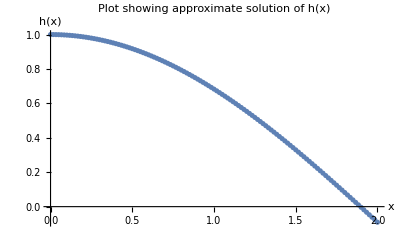

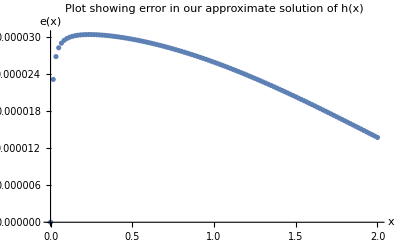

```mathematica
ListPlot[Transpose[{x,h}], PlotLabel ->"Plot showing approximate solution of h(x)", AxesLabel-> {"x","h(x)"}]
ListPlot[Transpose[{x,e}],PlotLabel ->"Plot showing error in our approximate solution of h(x)", AxesLabel-> {"x","e(x)"}]
```

The l_1 norm is given by ∑_(i=0)^N |e_i| 
The l_2 norm is given by √(∑_(i=0)^N (|e_i|)^2)

```mathematica
l1 = Sum[Abs[e[[i]]],{i,1,121}]
```

0.00293275

```mathematica
l2 = Sqrt[Sum[e[[i]]^2,{i,1,121}]]
```

0.000273636

Performing Hermite interpolation with 2 points inside (x[113],x[114]) and 2 points outside (x[115],x[116]) the star.

```mathematica
pmath[q_]:=InterpolatingPolynomial[
{{{x[[113]]},h[[113]],hp[x[[113]],m[[113]]]},
{{x[[114]]},h[[114]],hp[x[[114]],m[[114]]]},
{{x[[115]]},h[[115]],hp[x[[115]],m[[115]]]},
{{x[[116]]},h[[116]],hp[x[[116]],m[[116]]]}},q]
```

```mathematica
Rnumeric= FindRoot[pmath[q],{q,1.7}][[1]][[2]];
Rexact =1.8954942670339812;
error = Rnumeric - Rexact //N;
Print["Numeric R value= " ,Rnumeric]
Print["Exact R value= " ,Rexact]
Print["Error in our value =" ,error]
```

Numeric R value= 1.89551

Exact R value= 1.89549

Error in our value =0.0000175374